```mathematica
(* Filename: Time_By_w2_SSDFMT_tuck_A1_2A1_sym_DN
*)
(* Ver. 0 (28-Aug-2025) *)
(*
This file is used to prepare for a plot in Fig. 2.
*)
```

```mathematica
(***** In the following line, you need to set a path 
to the folder "For_figs_1_2". *****)
(*
datadir= "D:/.../For_figs_1_2/";
*)
```

```mathematica
nn=127;
```

```mathematica
mydirB4 = StringJoin[datadir,"/By_w2_SS_tuck_A1_2A1_sym_DN/dt=1_4/Se16_Tr1000_B256"];
(***)
mydirB8 = StringJoin[datadir,"/By_w2_SS_tuck_A1_2A1_sym_DN/dt=1_8/Se16_Tr1000_B256"];
(***)
mydirB16= StringJoin[datadir,"/By_w2_SS_tuck_A1_2A1_sym_DN/dt=1_16/Se16_Tr1000_B256"];
(***)
mydirB32 = StringJoin[datadir,"/By_w2_SS_tuck_A1_2A1_sym_DN/dt=1_32/Se16_Tr1000_B256"];
(***)
mydirB64 = StringJoin[datadir,"/By_w2_SS_tuck_A1_2A1_sym_DN/dt=1_64/Se16_Tr1000_B256"];
(***)
mydirA14 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_128/St14_Se16_Tr1000_B256"];
```

```mathematica
numSetForTime=16;
```

```mathematica
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirB4<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListB4={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirB4<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListB4=Append[timeListB4,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirB8<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListB8={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirB8<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListB8=Append[timeListB8,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirB16<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListB16={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirB16<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListB16=Append[timeListB16,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirB32<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListB32={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirB32<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListB32=Append[timeListB32,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirB64<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListB64={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirB64<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListB64=Append[timeListB64,locTmp];
];
```

```mathematica
numSubSetForTime=8;(* 1, 2, 4, 8, 16 *)
numMiniSet=numSetForTime/numSubSetForTime;
```

```mathematica
timeListB4SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListB4SubSum[[ll]]=timeListB4[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListB4SubSum[[ll]]+=timeListB4[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListB8SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListB8SubSum[[ll]]=timeListB8[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListB8SubSum[[ll]]+=timeListB8[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListB16SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListB16SubSum[[ll]]=timeListB16[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListB16SubSum[[ll]]+=timeListB16[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListB32SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListB32SubSum[[ll]]=timeListB32[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListB32SubSum[[ll]]+=timeListB32[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListB64SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListB64SubSum[[ll]]=timeListB64[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListB64SubSum[[ll]]+=timeListB64[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
```

```mathematica
timeB4Ave=Mean[timeListB4SubSum];
timeB4Std=Sqrt[Total[(timeListB4SubSum-timeB4Ave)^2]/numSubSetForTime];
(***)
timeB8Ave=Mean[timeListB8SubSum];
timeB8Std=Sqrt[Total[(timeListB8SubSum-timeB8Ave)^2]/numSubSetForTime];
(***)
timeB16Ave=Mean[timeListB16SubSum];
timeB16Std=Sqrt[Total[(timeListB16SubSum-timeB16Ave)^2]/numSubSetForTime];
(***)
timeB32Ave=Mean[timeListB32SubSum];
timeB32Std=Sqrt[Total[(timeListB32SubSum-timeB32Ave)^2]/numSubSetForTime];
(***)
timeB64Ave=Mean[timeListB64SubSum];
timeB64Std=Sqrt[Total[(timeListB64SubSum-timeB64Ave)^2]/numSubSetForTime];
```

```mathematica
tmpMini=Table[{},{ii,1,5}];
tmpMini[[1]]={Log[2,timeB4Ave],Log[2,1/4]};
tmpMini[[2]]={Log[2,timeB8Ave],Log[2,1/8]};
tmpMini[[3]]={Log[2,timeB16Ave],Log[2,1/16]};
tmpMini[[4]]={Log[2,timeB32Ave],Log[2,1/32]};
tmpMini[[5]]={Log[2,timeB64Ave],Log[2,1/64]};
listTimeBForAve=Table[tmpMini[[ii]],{ii,1,5}];
```

```mathematica
plotlistTimeBForAve=ListPlot[listTimeBForAve];
```

```mathematica
tmpStep=1/4;
plotMiniBarB4ForTime=ListPlot[{{Log[2,timeB4Ave+timeB4Std],Log[2,tmpStep]},{Log[2,timeB4Ave-timeB4Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarB8ForTime=ListPlot[{{Log[2,timeB8Ave+timeB8Std],Log[2,tmpStep]},{Log[2,timeB8Ave-timeB8Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarB16ForTime=ListPlot[{{Log[2,timeB16Ave+timeB16Std],Log[2,tmpStep]},{Log[2,timeB16Ave-timeB16Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarB32ForTime=ListPlot[{{Log[2,timeB32Ave+timeB32Std],Log[2,tmpStep]},{Log[2,timeB32Ave-timeB32Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarB64ForTime=ListPlot[{{Log[2,timeB64Ave+timeB64Std],Log[2,tmpStep]},{Log[2,timeB64Ave-timeB64Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
```

```mathematica
tmpUpperListB={{Log[2,timeB4Ave+timeB4Std],Log[2,1/4]},{Log[2,timeB8Ave+timeB8Std],Log[2,1/8]},{Log[2,timeB16Ave+timeB16Std],Log[2,1/16]},{Log[2,timeB32Ave+timeB32Std],Log[2,1/32]},{Log[2,timeB64Ave+timeB64Std],Log[2,1/64]}};
tmpLowerListB={{Log[2,timeB4Ave-timeB4Std],Log[2,1/4]},{Log[2,timeB8Ave-timeB8Std],Log[2,1/8]},{Log[2,timeB16Ave-timeB16Std],Log[2,1/16]},{Log[2,timeB32Ave-timeB32Std],Log[2,1/32]},{Log[2,timeB64Ave-timeB64Std],Log[2,1/64]}};
```

```mathematica
tmpLine=Line[{{0.,0.},{0,0.5}}];
tmpSize=5.0; (* 5.0, 10.0 *)
Graphics[{Gray(*RGBColor[0,0,1]*),tmpLine},AspectRatio->NCache[GoldenRatio^(-1),0.6180339887498948],Axes->None,AxesOrigin->{0,0},ImageSize->{tmpSize,Automatic},Method->{},PlotRange->{{0,0},{0,0.5}},PlotRangeClipping->True,PlotRangePadding->{{0.,0.},{0.01,0.01}}]
```

-Graphics-

```mathematica
plotMarkerListBForTime=ListPlot[{tmpLowerListB,tmpUpperListB},PlotMarkers->{"",""}(*,PlotMarkers->{"",""}*)];
```

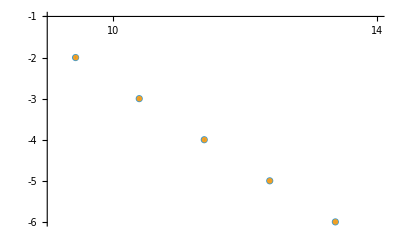

```mathematica
ll=0.015;
Show[plotlistTimeBForAve,plotMarkerListBForTime,plotMiniBarB4ForTime,plotMiniBarB8ForTime,plotMiniBarB16ForTime,plotMiniBarB32ForTime,plotMiniBarB64ForTime,PlotRange->{{9+0.05,14}(*{10.85,10.9}*),{-6,-1}},AxesOrigin->{9,-1},Ticks->{Table[{1ii,ToString[1ii],ll},{ii,2,20}],Table[{-1ii,ToString[-1ii],ll},{ii,1,6}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```